# Title

Peter Burbery

Abstract

## Section

XXXX:

## Boolean

```mathematica
myboolean=BooleanFunction[234,3]
```

BooleanFunction[…]

```mathematica
BooleanTable[myboolean]
```

{True,True,True,False,True,False,True,False}

```mathematica
BooleanVariables[myboolean]
```

3

```mathematica
UnateQ[myboolean]
```

True

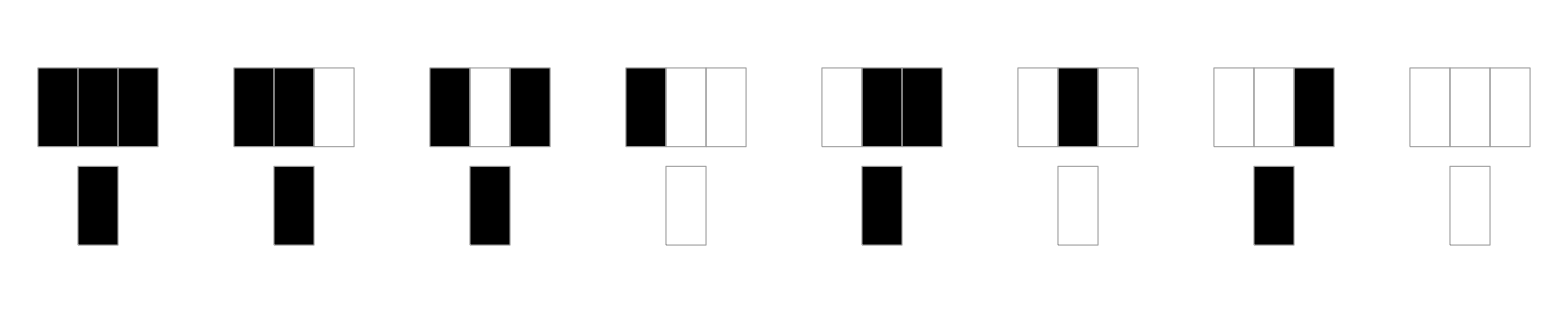

```mathematica
RulePlot[myboolean]
```

```mathematica
AssociationThread[{"DNF","SOP","CNF","POS",
"ESOP","ANF","NOR","NAND","AND","OR","IMPLIES",
"OR","IMPLIES","ITE","IF","BFF","BDT"},BooleanConvert[myboolean,{"DNF","SOP","CNF","POS",
"ESOP","ANF","NOR","NAND","AND","OR","IMPLIES",
"OR","IMPLIES","ITE","IF","BFF","BDT"}]]
```

<|DNF→((#1&&#2)||#3&),SOP→((#1&&#2)||#3&),CNF→((#1||#3)&&(#2||#3)&),POS→((#1||#3)&&(#2||#3)&),ESOP→((#1&&#2&&!#3)⊻#3&),ANF→((#1&&#2)⊻(#1&&#2&&#3)⊻#3&),NOR→((#1⊽#3)⊽(#2⊽#3)&),NAND→((#1⊼#2)⊼!#3&),AND→(!(!#1&&!#3)&&!(!#2&&!#3)&),OR→(!(!#1||!#2)||#3&),IMPLIES→((#1⇒!(!#2⇒#3))⇒!(!#1⇒!#3)&),ITE→(If[#1,If[#2,True,If[#3,True,False]],If[#3,True,False]]&),IF→(If[#1,If[#2,True,If[#3,True,False]],If[#3,True,False]]&),BFF→BooleanFunction[…],BDT→((#1&&(#2||(!#2&&#3)))||(!#1&&#3)&)|>

```mathematica
AssociationThread[{"DNF","SOP","CNF","POS",
"ANF","NOR","NAND","AND","OR"},BooleanMinimize[myboolean,{"DNF","SOP","CNF","POS",
"ANF","NOR","NAND","AND","OR"}]]
```

<|DNF→((#1&&#2)||#3&),SOP→((#1&&#2)||#3&),CNF→((#1||#3)&&(#2||#3)&),POS→((#1||#3)&&(#2||#3)&),ANF→((#1&&#2)⊻(#1&&#2&&#3)⊻#3&),NOR→((#1⊽#3)⊽(#2⊽#3)&),NAND→((#1⊼#2)⊼!#3&),AND→(!(!#1&&!#3)&&!(!#2&&!#3)&),OR→(!(!#1||!#2)||#3&)|>

```mathematica
AssociationThread[{"DNF","SOP","CNF","POS",
"ESOP","ANF","NOR","NAND","AND","OR","IMPLIES",
"OR","IMPLIES","ITE","IF","BFF","BDT"},LeafCount/@BooleanConvert[myboolean,{"DNF","SOP","CNF","POS",
"ESOP","ANF","NOR","NAND","AND","OR","IMPLIES",
"OR","IMPLIES","ITE","IF","BFF","BDT"}]]
```

<|DNF→9,SOP→9,CNF→12,POS→12,ESOP→12,ANF→16,NOR→12,NAND→10,AND→18,OR→12,IMPLIES→20,ITE→18,IF→18,BFF→1,BDT→20|>

```mathematica
AssociationThread[{"DNF","SOP","CNF","POS",
"ANF","NOR","NAND","AND","OR"},LeafCount/@BooleanMinimize[myboolean,{"DNF","SOP","CNF","POS",
"ANF","NOR","NAND","AND","OR"}]]
```

<|DNF→9,SOP→9,CNF→12,POS→12,ANF→16,NOR→12,NAND→10,AND→18,OR→12|>

## Dont cares

```mathematica
AssociationThread[{"DNF","SOP","CNF","POS",
"ANF","NOR","NAND","AND","OR"},BooleanMinimize[(a∨¬b∧
c∧¬d)∨(a∧b∧¬c∧¬d)∨(a∧b∧c∧¬d)
,{"DNF","SOP","CNF","POS",
"ANF","NOR","NAND","AND","OR"}]]
```

<|DNF→a||(!b&&c&&!d),SOP→a||(!b&&c&&!d),CNF→(a||!b)&&(a||c)&&(a||!d),POS→(a||!b)&&(a||c)&&(a||!d),ANF→a⊻c⊻(a&&c)⊻(b&&c)⊻(c&&d)⊻(a&&b&&c)⊻(a&&c&&d)⊻(b&&c&&d)⊻(a&&b&&c&&d),NOR→(a⊽!b)⊽(a⊽c)⊽(a⊽!d),NAND→!a⊼(!b⊼c⊼!d),AND→!(!a&&b)&&!(!a&&!c)&&!(!a&&d),OR→a||!(b||!c||d)|>

```mathematica
AssociationThread[{"DNF","SOP","CNF","POS",
"ANF","NOR","NAND","AND","OR"},BooleanMinimize[(a∨¬b∧
c∧¬d)∨(a∧b∧¬c∧¬d)∨(a∧b∧c∧¬d)
,{"DNF","SOP","CNF","POS",
"ANF","NOR","NAND","AND","OR"}]]//TraditionalForm
```

<|DNF→a∨(¬b∧c∧¬d),SOP→a∨(¬b∧c∧¬d),CNF→(a∨¬b)∧(a∨c)∧(a∨¬d),POS→(a∨¬b)∧(a∨c)∧(a∨¬d),ANF→a⊻c⊻(a∧c)⊻(b∧c)⊻(c∧d)⊻(a∧b∧c)⊻(a∧c∧d)⊻(b∧c∧d)⊻(a∧b∧c∧d),NOR→(a⊽¬b)⊽(a⊽c)⊽(a⊽¬d),NAND→¬a⊼(¬b⊼c⊼¬d),AND→¬(¬a∧b)∧¬(¬a∧¬c)∧¬(¬a∧d),OR→a∨¬(b∨¬c∨d)|>

```mathematica
LogicalExpand[a∨(¬b∧c∧¬d)]
```

a||(c&&!b&&!d)

```mathematica
BooleanMinimize[LogicalExpand[a∨(¬b∧c∧¬d)]]
```

a||(!b&&c&&!d)

```mathematica
BooleanMinimize[BooleanFunction[{{1,0,1,0}->1,{1,0,1,1}->0,{1,1,0,0}->1,{1,1,0,1}->0,{1,1,1,0}->1,{1,1,1,1}->0},{a,b,c,d}],"SOP" (* ="DNF"*),BooleanFunction[{{1,1,_,_}->1,(*all cases above...*){1,_,1,_}->1,(*... are "do care"*){_,_,_,_}->0 (*other cases are "don't care"*)},{a,b,c,d}]]
```

!d

```mathematica
BooleanMinimize[BooleanFunction[{{1,0,1,0}->1,{1,0,1,1}->0,{1,1,0,0}->1,{1,1,0,1}->0,{1,1,1,0}->1,{1,1,1,1}->0},{a,b,c,d}],"SOP" (* ="DNF"*),BooleanFunction[{{1,1,_,_}->1,(*all cases above...*){1,_,1,_}->1,(*... are "do care"*){_,_,_,_}->0 (*other cases are "don't care"*)},{a,b,c,d}]]//TraditionalForm
```

¬d

```mathematica
IntegerDigits[Range[10]]
```

{{1},{2},{3},{4},{5},{6},{7},{8},{9},{1,0}}

```mathematica
IntegerDigits[Range[10],2]
```

{{1},{1,0},{1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1},{1,0,0,0},{1,0,0,1},{1,0,1,0}}

```mathematica
IntegerDigits[Range[10],2^4]
```

{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10}}

```mathematica
IntegerDigits[Range[10],2]
```

{{1},{1,0},{1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1},{1,0,0,0},{1,0,0,1},{1,0,1,0}}

```mathematica
IntegerDigits[Range[2^4],2]
```

{{1},{1,0},{1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1},{1,0,0,0},{1,0,0,1},{1,0,1,0},{1,0,1,1},{1,1,0,0},{1,1,0,1},{1,1,1,0},{1,1,1,1},{1,0,0,0,0}}

```mathematica
PadLeft[#,5]&/@IntegerDigits[Range[2^4],2]
```

{{0,0,0,0,1},{0,0,0,1,0},{0,0,0,1,1},{0,0,1,0,0},{0,0,1,0,1},{0,0,1,1,0},{0,0,1,1,1},{0,1,0,0,0},{0,1,0,0,1},{0,1,0,1,0},{0,1,0,1,1},{0,1,1,0,0},{0,1,1,0,1},{0,1,1,1,0},{0,1,1,1,1},{1,0,0,0,0}}

```mathematica
PadLeft[#,4]&/@IntegerDigits[Range[2^3],2]
```

{{0,0,0,1},{0,0,1,0},{0,0,1,1},{0,1,0,0},{0,1,0,1},{0,1,1,0},{0,1,1,1},{1,0,0,0}}

```mathematica
{#,PadLeft[IntegerDigits[#,2],4]}&/@Range[2^3]
```

{{1,{0,0,0,1}},{2,{0,0,1,0}},{3,{0,0,1,1}},{4,{0,1,0,0}},{5,{0,1,0,1}},{6,{0,1,1,0}},{7,{0,1,1,1}},{8,{1,0,0,0}}}

## New plan

List of functions

Truth table

alternative boolean forms with FindBooleanAlternative

Karnaugh map for four variables, hardcoded with example above. hope to add support for others like five variables later.

Venn diagram

Inverse boole converts 1 to true and 0 to false.

boolean summary.

allbutonetrue useful for testing if something is unique. help with AllTrue, AnyTrue, NoneTrue.

```mathematica
booleanstructuredata[func_]:=<|
"truthtable"->BooleanTable[func],"truthvector"->
Boole[BooleanTable[func]],"variables"->
BooleanVariables[func],"monotone"->UnateQ[func]|>
```

```mathematica
booleansummary[BooleanFunction[100,5]]
```

<|truthtable→{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,True,False,False},truthvector→{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,1,0,0},variables→5,monotone→False|>

```mathematica
booleantestdata[func_]:=<|"satisfiable"->
SatisfiableQ[func],"truecount"->SatisfiabilityCount[func],
"trueinstances"->SatisfiabilityInstances[func],
"tautology"->TautologyQ[func]|>
```

```mathematica
booleanpredicatedata[func_]:=<|"resolved"->
Resolve[func],"reduced"->Reduce[func],"expanded"->
LogicalExpand[func]|>
```

```mathematica
booleantestdata[BooleanFunction[100,5]]
```

<|satisfiable→True,truecount→3,trueinstances→{{False,False,False,True,False}},tautology→False|>

```mathematica
booleantestdata[BooleanFunction[1000,12]]
```

<|satisfiable→True,truecount→6,trueinstances→{{False,False,False,False,False,False,False,False,True,False,False,False}},tautology→False|>

```mathematica
booleanpredicatedata[∀_x c+b x+a x^2>0]
```

<|resolved→(b|c)∈ℝ&&((a==0&&b==0&&c>0)||(a≥0&&b==0&&c>0&&-b^2+4 a c>0)||(a>0&&-b^2+4 a c>0)),reduced→c>0&&((b<0&&a>b^2/(4 c))||(b==0&&a≥0)||(b>0&&a>b^2/(4 c))),expanded→∀_x c+b x+a x^2>0|>

```mathematica
booleanpredicatedata[∀_x c+b x+a x^2>0]//TraditionalForm
```

<|resolved→(b|c)∈ℝ∧((a==0∧b==0∧c>0)∨(a≥0∧b==0∧c>0∧4 a c-b^2>0)∨(a>0∧4 a c-b^2>0)),reduced→c>0∧((b<0∧a>b^2/(4 c))∨(b==0∧a≥0)∨(b>0∧a>b^2/(4 c))),expanded→∀_x a x^2+b x+c>0|>

```mathematica
booleanpredicatedata[∀_x 1-x+x^2≠0]//TraditionalForm
```

<|resolved→False,reduced→False,expanded→∀_x x^2-x+1≠0|>

```mathematica
booleanpredicatedata[∀_(x,x∈Reals)1-x+x^2≠0]//TraditionalForm
```

<|resolved→True,reduced→True,expanded→∀_(x,x∈ℝ)x^2-x+1≠0|>

```mathematica
booleanpredicatedata[∀_{x,y}x^2+y^2≥0]//TraditionalForm
```

<|resolved→True,reduced→True,expanded→∀_{x,y}x^2+y^2≥0|>

```mathematica
booleanpredicatedata[∀_{p,q}(p&&(p⇒q)⇒q)]//TraditionalForm
```

<|resolved→True,reduced→True,expanded→∀_{p,q}(p∧(p⇒q)⇒q)|>

```mathematica
booleanpredicatedata[∀_({a,b},a>0&&b>0)(a+b)/2≥√(a b)]//TraditionalForm
```

<|resolved→True,reduced→True,expanded→∀_({a,b},a>0∧b>0)(a+b)/2≥√(a b)|>

```mathematica
booleanpredicatedata[∀_({a,b,c,d},a>0&&b>0&&c>0&&d>0)a c+b d≤√(a^2+b^2) √(c^2+d^2)]//TraditionalForm
```

<|resolved→True,reduced→True,expanded→∀_({a,b,c,d},a>0∧b>0∧c>0∧d>0)a c+b d≤√(a^2+b^2) √(c^2+d^2)|>

```mathematica
booleanpredicatedata[∀_{a,b,c,d}√((a+c)^2+(b+d)^2)≤√(a^2+b^2)+√(c^2+d^2)]//TraditionalForm
```

<|resolved→True,reduced→True,expanded→∀_{a,b,c,d}√((a+c)^2+(b+d)^2)≤√(a^2+b^2)+√(c^2+d^2)|>

```mathematica
booleanpredicatedata[∀_({a,b,c},a>0&&b>0&&c>0&&a+b>c&&a+c>b&&b+c>a)a b c (a^2/b^2+b^2/c^2+c^2/a^2)≥a^3+b^3+a b (-a+b)+a (a-c) c+c^3+b c (-b+c)]//TraditionalForm
```

<|resolved→True,reduced→True,expanded→∀_({a,b,c},a>0∧b>0∧c>0∧a+b>c∧a+c>b∧b+c>a)a b c (a^2/b^2+c^2/a^2+b^2/c^2)≥a^3+a b (b-a)+a c (a-c)+b^3+b c (c-b)+c^3|>

```mathematica
booleanpredicatedata[∀_({a,b,c},a>0&&b>0&&c>0&&a+b>c&&a+c>b&&b+c>a&&a^2+b^2>c^2&&a^2+c^2>b^2&&b^2+c^2>a^2)27 (a^2+b^2-c^2)^2 (a^2-b^2+c^2)^2 (-a^2+b^2+c^2)^2≤512 (a+b+c)^3 (-a+1/2 (a+b+c))^3 (-b+1/2 (a+b+c))^3 (-c+1/2 (a+b+c))^3]//TraditionalForm
```

<|resolved→True,reduced→True,expanded→∀_({a,b,c},a>0∧b>0∧c>0∧a+b>c∧a+c>b∧b+c>a∧a^2+b^2>c^2∧a^2+c^2>b^2∧b^2+c^2>a^2)27 (a^2+b^2-c^2)^2 (a^2-b^2+c^2)^2 (-a^2+b^2+c^2)^2≤512 (a+b+c)^3 (1/2 (a+b+c)-a)^3 (1/2 (a+b+c)-b)^3 (1/2 (a+b+c)-c)^3|>

```mathematica
BooleanStructure
```

```mathematica
BooleanConvert[BooleanFunction[100,3],"BFF"]
```

BooleanFunction[…]

```mathematica
BooleanConvert[a∧b∧c,"BFF"]
```

BooleanFunction[…][a,b,c]

```mathematica
BooleanVariables[BooleanFunction[…][a,b,c]]
```

{a,b,c}

```mathematica
BooleanVariables[BooleanConvert[BooleanFunction[100,3],"BFF"]]
```

3

```mathematica
ExpressionTree[Defer[BooleanVariables[BooleanFunction[…]]]]
```

-Graphics-

```mathematica
ExpressionTree[Defer[BooleanFunction[…][a,b,c]]]
```

-Graphics-

```mathematica
ExpressionTree[Defer[BooleanFunction[…]]]
```

-Graphics-

```mathematica
UnateQ[BooleanFunction[…][a,b,c],{False,False,False}]
```

UnateQ[BooleanFunction[…][a,b,c],{False,False,False}]

```mathematica
UnateQ[BooleanFunction[…][a,b,c],{_,_,¬c}]
```

False

```mathematica
UnateQ[BooleanFunction[…][a,b,c],{_,¬b,¬c}]
```

False

```mathematica
UnateQ[BooleanFunction[…][a,b,c],{¬a,¬b,¬c}]
```

False

```mathematica
UnateQ[BooleanFunction[…][a,b,c],{a,b,c}]
```

True